# Real Analysis, Lecture 10

## Allianz Presentation 3-4 pm next Thursday (probably in CC 230)

## What are Limsups and Liminfs good for?

### Does ∑ _(k=1)^∞ (2+(-1)^k)*2^-k=1/2+3/4+1/8+3/16+1/32+3/64+··· converge?

```mathematica
a[k_]:=(2+(-1)^(k))*2^(-k)
```

```mathematica
DiscretePlot[a[k],{k,1,20},PlotRange->{0,.8},PlotStyle->Red]
```

```mathematica
∑_(k=1)^∞ a[k]
```

### Can this be proved? With the Ratio Test? With the Root Test?

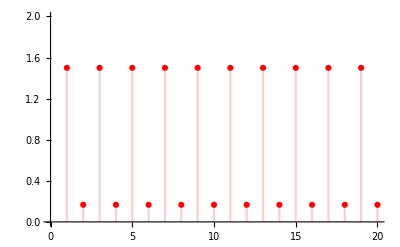

```mathematica
DiscretePlot[a[k+1]/a[k],{k,1,20},PlotRange->{0,2},PlotStyle->Red]
```

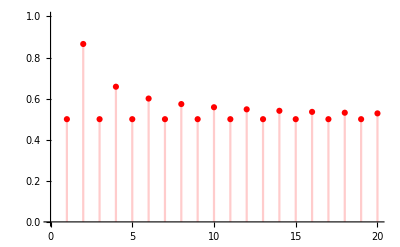

```mathematica
DiscretePlot[a[k]^(1/k),{k,1,20},PlotRange->{0,1},PlotStyle->Red]
```

## A Reminder to Expect the Unexpected

```mathematica
Manipulate[Plot[Sin[1/x]/x,{x,-a,a},PlotStyle->{Thick,Red},PerformanceGoal->"Quality"],{a,1,.001,-.001}]
```

```mathematica
Manipulate[Plot[(√(x^2+9)-3)/x^2,{x,-a,a},PlotStyle->{Thick,Red},PerformanceGoal->"Quality"],{a,1,.001,-.001}]
```

## Limits of Functions Defined on Open Intervals (possibly with one point removed)

```mathematica
g[x_]:=x^2;h[x_]:=1/x;Invg[x_]:=√x;Invh[x_]:=h[x];Manipulate[Show[Plot[f[x],{x,0,2},PlotStyle->{Thick,Black}],Graphics[{Thick,Red,Line[{{0,f[c]+ϵ},{Invf[f[c]+ϵ],f[c]+ϵ}}]}],Graphics[{Thick,Red,Line[{{0,f[c]-ϵ},{Invf[f[c]-ϵ],f[c]-ϵ}}]}],Graphics[{Thick,Green,Line[{{0,f[c]},{c,f[c]},{c,0}}]}],Graphics[{Thick,Blue,Line[{{c-δ,0},{c-δ,f[c-δ]}}]}],Graphics[{Thick,Blue,Line[{{c+δ,0},{c+δ,f[c+δ]}}]}],PlotRange->{-1,5},AspectRatio->1],{f,{g,h}},{Invf,{Invg,Invh}},{c,.51,2},{ϵ,.2,.01},{δ,.5,.001}]
```

## Relation to Limits of Sequences

## Algebraic Properties and the Squeeze Theorem

## One-Sided Limits and Other Kinds of Limits

## Continuity and Discontinuity